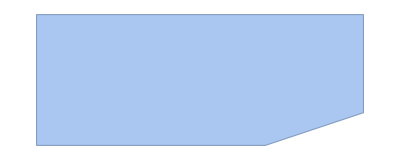

```mathematica
Clear["Global`*"];
height=4.;
width=10.;
inclined=7.;
inheight=1.;
OuterRegion=BoundaryMeshRegion[{
{0,0},{inclined,0},{width,inheight},{width,height},{0,height}
},Line[{1,2,3,4,5,1}]];
OuterRegion
```

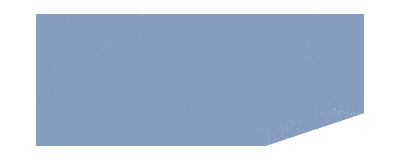

```mathematica
mesh=TriangulateMesh[OuterRegion,MaxCellMeasure->0.003]
```

```mathematica
Export["C:\\Users\\bcynuaa\\Desktop\\mesh.ply",mesh];
```